## TensorPairContract Benchmarks

```mathematica
Needs["QuantumUtils`"]
```

## Benchmark Size of Square Tensor Multiplication

```mathematica
FirstTensor[numberOfPoints_] := With[
{n = numberOfPoints},
Array[RandomComplex, {n, n}]
];
```

```mathematica
SecondTensor[numberOfPoints_] := With[
{n = numberOfPoints},
Array[RandomComplex, {n, n}]
];
```

```mathematica
Benchmark[numberOfPoints_] := With[
{a = FirstTensor[numberOfPoints], b = SecondTensor[numberOfPoints]},
AbsoluteTiming[TensorPairContract[a, b, {1, 1}]][[1]]
];
```

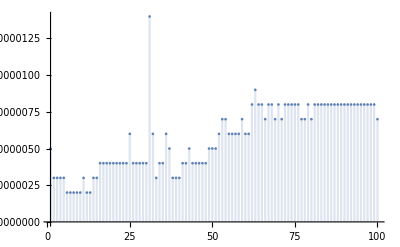

```mathematica
DiscretePlot[Benchmark[n], {n, 1, 1000}]
```

```mathematica
T = Array[a, {2, 2}]
```

{{a[1,1],a[1,2]},{a[2,1],a[2,2]}}

```mathematica
V = Array[a, {2, 2}]
```

{{a[1,1],a[1,2]},{a[2,1],a[2,2]}}

```mathematica
TensorPairContract[T, V, {{1, 1}}]
```

{{a[1,1]^2+a[2,1]^2,a[1,1] a[1,2]+a[2,1] a[2,2]},{a[1,1] a[1,2]+a[2,1] a[2,2],a[1,2]^2+a[2,2]^2}}

```mathematica
T . V
```

{{a[1,1]^2+a[1,2] a[2,1],a[1,1] a[1,2]+a[1,2] a[2,2]},{a[1,1] a[2,1]+a[2,1] a[2,2],a[1,2] a[2,1]+a[2,2]^2}}